# npn-Transistor

## Funktionen

### Includes

```mathematica
Needs["ErrorBarPlots`"]
```

### Fehlerfunktion(Größtfehler) ∑(|df/dx_i|Δx_i)

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
```

### Gaussfunktion

```mathematica
Gauss[a_]:={Mean[a],StandardDeviation[a]/(√Length[a])}
```

### Basics

```mathematica
fAdd[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a+b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

```mathematica
Fdiv[a1_,da1_,b1_,db1_]:= Module[{f,fe,a,b,da,db},
f=a/b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->a1,da->da1,b-> b1,db->db1}]
```

```mathematica
Fmult[γ_,dγ_,δ_,dδ_]:= Module[{f,fe,a,b,da,db},
f=a*b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->γ,da->dγ,b-> δ,db->dδ}]
```

```mathematica
Ff[a1_,da1_,b1_,db1_,c1_,dc1_]:= Module[{f,fe,a,b,c,da,db,dc},
f=a*b/c;
fe = GError[f,{a,b,c},{da,db,dc}];
{f,fe}/.{a->a1,da->da1,b-> b1,db->db1,c->c1,dc->dc1}]
```

## Vorlage

-Graphics-

## 1.) Vierquadrantenkennlinienfeld eines npn-Transistors

```mathematica
i20 =19.9 *10^-6;
i50 = 50.1 *10^-6;
i100=100.5 *10^-6;
```

```mathematica
ti20={{"U_CE", "I_C", "U_BE"}, {0.002, -0.8, 0.541}, {1.023, 269.4, 0.573}, {2.008, 536, 0.589}, {3.276, 880, 0.600}, {4.070, 1095, 0.605}, {5.105, 1377, 0.612}, {6.124, 1655, 0.616}, {7.07, 1912, 0.620}, {8.07, 2177, 0.624}, {9.08, 2260, 0.625}, {10.02, 2270, 0.624}};
ti50={{"U_CE", "I_C", "U_BE"}, {0.003, -0.5, 0.566}, {1.112, 296.0, 0.584}, {2.152, 575.9, 0.593}, {3.215, 866, 0.601}, {4.027, 1086, 0.606}, {5.037, 1362, 0.610}, {5.997, 1624, 0.614}, {7.09, 1924, 0.618}, {8.14, 2213, 0.621}, {9.00, 2452, 0.623}, {10.11, 2761, 0.626}};
ti100={{"U_CE", "I_C", "U_BE"}, {0.002, -0.6, 0.588}, {1.053, 284.4, 0.597}, {2.001, 542.3, 0.603}, {3.025, 822, 0.609}, {4.067, 1108, 0.613}, {5.121, 1396, 0.617}, {6.081, 1660, 0.620}, {7.13, 1949, 0.623}, {8.06, 2209, 0.625}, {9.10, 2500, 0.628}, {10.06, 2766, 0.630}};
```

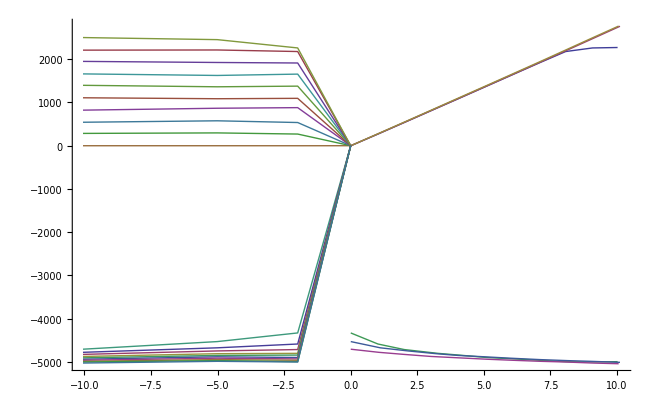

```mathematica
λ1=1;
λ2=1;
λ3=20^3;
λ4=10^5;
p201=Table[{λ1*ti20[[x,1]],λ2*ti20[[x,2]]},{x,2,12}];p202=Table[{λ1*ti20[[x,1]],-λ3 ti20[[x,3]]},{x,2,12}];
p501=Table[{λ1*ti50[[x,1]],λ2*ti50[[x,2]]},{x,2,12}];p502=Table[{λ1*ti50[[x,1]],-λ3 ti50[[x,3]]},{x,2,12}];
p1001=Table[{λ1*ti100[[x,1]],λ2*ti100[[x,2]]},{x,2,12}];p1002=Table[{λ1*ti100[[x,1]],-λ3 ti100[[x,3]]},{x,2,12}];
p3=Table[{{0,0},{-λ4 i20,ti20[[x,2]]},{-λ4 i50,ti50[[x,2]]},{-λ4 i100,ti100[[x,2]]}},{x,2,12}];
p4=Table[{{0,0},{-λ4 i20,- λ3 ti20[[x,3]]},{-λ4 i50,- λ3 ti50[[x,3]]},{-λ4 i100,- λ3 ti100[[x,3]]}},{x,2,12}];
Show[ListPlot[{p201,p501,p1001,p202,p502,p1002,p3[[1]],p3[[2]],p3[[3]],p3[[4]],p3[[5]],p3[[6]],p3[[7]],p3[[8]],p3[[9]],p3[[10]],p4[[1]],p4[[2]],p4[[3]],p4[[4]],p4[[5]],p4[[6]],p4[[7]],p4[[8]],p4[[9]],p4[[10]]},Joined->True],PlotRange->{{-12,10},{3000,-5000}}]
```

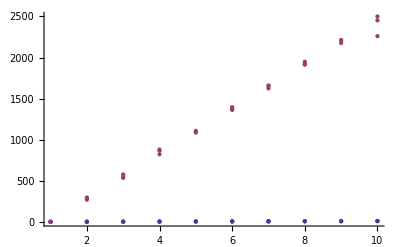

```mathematica
Show[ListPlot[{ti20[[2;;11,1]],ti20[[2;;11,2]]}],ListPlot[{ti50[[2;;11,1]],ti50[[2;;11,2]]}],ListPlot[{ti100[[2;;11,1]],ti100[[2;;11,2]]}]]
```

```mathematica
dti20= Table[{ti20[[x,1]]*0.01+0.001,ti20[[x,2]]*0.015+0.01},{x,2,Length[ti20]}];
dti50= Table[{ti50[[x,1]]*0.01+0.001,ti50[[x,2]]*0.015+0.01},{x,2,Length[ti50]}];
dti100= Table[{ti100[[x,1]]*0.01+0.001,ti100[[x,2]]*0.015+0.01},{x,2,Length[ti100]}];
```

```mathematica
(*p1 = Table[{{dt[[x,1]],dt[[x,2]]},ErrorBar[ddt[[x,1]],ddt[[x,2]]]},{x,1,Length[dt]}]
ErrorListPlot[p1,Joined-> True,AxesOrigin-> {0,0},AxesLabel-> {"U/V","I/mA"},PlotRange->{{0,0.8},{0,140}}]*)
```

## 2.) Transistor-Verstärkerschaltung

```mathematica
(*ic = {{5, 1}}*10^-3;   ka was ich da aufgschrieben hab ^^*)
tv1 = {{"U_E", "U_A"}, {20, 2*3.4*0.5}, {30, 2*2.5*1}, {40, 1.8*4}, {50, 4.8*2}};
tv2 = {{"U_E", "U_A"}, {20, 1.6*2}, {30, 3.4*2}, {40, 4.5*2}, {50, 4.8*2}};
i1=1*10^-3;
i2 = 2.4*10^-3;
```